# Ereignishorizonte r_± finden

Dieses Worksheet basiert auf keinem alten Worksheet (nicht direkt jedenfalls) und versucht, die Event Horizon Equation g_00=0 zu lösen, für Holo und Self-Encoding Hα.

## Holo, neu

Am besten leitet man die Polynome der Lsg g_00=0, also V(r)=1, mit der Hand her, weil sie bei Mathematica nicht hübsch werden. So findet man fuer Holo

```mathematica
fholo[z_,m_,n_] = z^(2+n) - z m + 1
```

1-m z+z^(2+n)

Man kann nette Sachen machen mit der Taylorentwicklung um das Minimum herum, was man per ∂_r f(r)=0 leicht findet für holo.

```mathematica
xmin=(m / (n+2))^(1/(1+n))
```

(m/(2+n))^(1/(1+n))

```mathematica
fholoapprox[z_,m_,n_]=Refine[Series[fholo[z,m,n],{z,xmin,2}] ,n>0 ∧m>0] // FullSimplify // Normal
```

1-(1+n) (m/(2+n))^(1+1/(1+n))+1/2 (1+n) (m/(2+n))^(n/(1+n)) (2+n) (-(m/(2+n))^(1/(1+n))+z)^2

Das kann man plotten, um (mal wieder) zu sehen, dass für z>0 keine, eine oder zwei Lösungen möglich sind. Man sieht sofort, dass es eine ganz harmlose Funktion ist:

```mathematica
Manipulate[Plot[Evaluate@{fholo[z,m,n],fholoapprox[z,m,n]}, {z,-4,4},PlotRange-> {-1,4}],
{{m,1},0,4},{n,0,7,1}]
```

## Hα neu

```mathematica
falpha[z_,m_,n_,a_] = z^2(z^a-1/2)^((3+n)/a)-m
```

-m+z^2 (-1/2+z^a)^((3+n)/a)

```mathematica
(* Re wg numerisch instabil*)
Manipulate[Plot[Re@falpha[z,m,n,a], {z,-4,4},PlotRange-> {-2,2}],
{m,0,4},{n,0,7,1},{{a,4},0,8}]
```

Hier scheint so eine Approximation nicht so leicht zu gehen. Mal wieder ist h_α unglaublich hässlich.

## Holo, Alt

Bei n=0 ist die Lösung einfach (quadratische Gleichung), bei n>0 hingegen wird sie richtig schwer.

```mathematica
h[z_,n_] = 1/(1+(1/z)^(2+n));
horizoneq[n_,H_] := m  H[z,n]/z^(1+n)-1
refinements = (AM)∈Reals∧AM>0 ∧n∈Integers ∧n≥0;
```

Ein Plot, um das ganze mal fuer verschiedene Massen und Dimensionen zu sehen:

```mathematica
Manipulate[Plot[(k z^(-1-n))/(1+z^(-2-n))-1, {z,0,10},PlotRange-> {-1,1}],{k,0,10},{n,0,10}]
```

### Lösungen

```mathematica
horizoneq[0,h]==0
horizoneq[0,h]==0// Simplify
Solve[horizoneq[0,h]==0,z] // FullSimplify
```

-1+m/((1+1/z^2) z)==0

(m z)/(1+z^2)==1

{{z→1/2 (m-√(-4+m^2))},{z→1/2 (m+√(-4+m^2))}}

```mathematica
$Assumptions={ Im@m == 0, Re@m > 0};
```

```mathematica
Reduce[0 == horizoneq[1,h],z] // ToRadicals
```

(z==((2/3)^(1/3) m)/((-9+√3 √(27-4 m^3))^(1/3))+((-9+√3 √(27-4 m^3))^(1/3))/(2^(1/3) 3^(2/3))||z==-((1+ⅈ √3) m)/(2^(2/3) 3^(1/3) (-9+√3 √(27-4 m^3))^(1/3))-((1-ⅈ √3) (-9+√3 √(27-4 m^3))^(1/3))/(2 2^(1/3) 3^(2/3))||z==-((1-ⅈ √3) m)/(2^(2/3) 3^(1/3) (-9+√3 √(27-4 m^3))^(1/3))-((1+ⅈ √3) (-9+√3 √(27-4 m^3))^(1/3))/(2 2^(1/3) 3^(2/3)))&&m z≠0

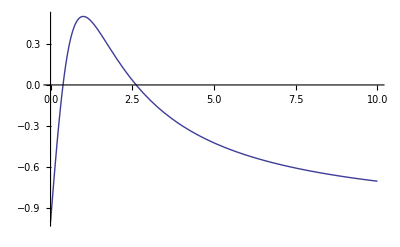

```mathematica
Plot[horizoneq[0,h] /. {z-> z, m-> 3}, {z,0,10}]
```